```mathematica
{NotebookFileName[],DateString[]}
```

{D:\WSL\morpheus\worm3\worm3.nb,Sun 7 Mar 2021 06:09:02}

## Setup

```mathematica
Needs["Developer`"]
```

```mathematica
$HistoryLength=5
```

5

```mathematica
curDir=FileNameDrop[NotebookFileName[]]
```

D:\WSL\morpheus\worm3

```mathematica
modelName=FileNameTake[curDir,-1]
```

worm3

```mathematica
logFile="logger.csv"
```

logger.csv

## Sweep 13

```mathematica
sweep=13
```

13

```mathematica
sweepDir=FileNameJoin[{curDir,modelName<>"_sweep_"<>ToString[sweep]}]
```

D:\WSL\morpheus\worm3\worm3_sweep_13

```mathematica
sweeps=FileNames[modelName<>"*",sweepDir];
```

```mathematica
"sweeps"<>ToString[sweep]<>"=sweeps"
```

sweeps13=sweeps

```mathematica
ToExpression[
"sweeps"<>ToString[sweep]<>"=sweeps"
]
```

{D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_166,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_167,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_168,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_169,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_170,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_171,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_172,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_173,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_174,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_175,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_176,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_177,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_178,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_179,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_180,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_181,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_182,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_183,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_184,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_185,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_186,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_187,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_188,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_189,D:\WSL\morpheus\worm3\worm3_sweep_13\worm3_190}

```mathematica
sweep13a=Import[
FileNameJoin[{sweeps13⟦1⟧,logFile}],
{"CSV","Dataset"}
,HeaderLines->1
]
```

```mathematica
sweep13a⟦1⟧["MKtemp"]
```

0.4

```mathematica
sweep13a⟦1⟧//Keys
```

```mathematica
sweep13a[GroupBy["time"]]⟦-1⟧
```

```mathematica
sweep13a[GroupBy["time"]]⟦-1⟧[StandardDeviation]
```

```mathematica
estimateVelocityDiffusion[
sweepDir_String,
logName_:logFile
]:=Module[{sweepds,tfinal,temp,cms,μx,μy,σx,σy},
sweepds=Import[
FileNameJoin[{sweepDir,logName}],
{"CSV","Dataset"}
,HeaderLines->1
];
sweepds=sweepds[GroupBy["time"]]⟦-1⟧;
temp=sweepds⟦1⟧["MKtemp"];
cms=sweepds⟦1⟧["cmstrength"];
tfinal=sweepds⟦1⟧["time"];
{σx,σy}=sweepds[All,{"delta_r.x","delta_r.y"}][StandardDeviation]/@{"delta_r.x","delta_r.y"};
{μx,μy}=sweepds[All,{"delta_r.x","delta_r.y"}][Mean]/@{"delta_r.x","delta_r.y"};
<|
"cmstrength"->cms,
"temperature"->temp,
"tfinal"->tfinal,
"vmean"->μx/tfinal,
"Dx"->σx^2/(2tfinal),
"Dy"->σy^2/(2tfinal),
"Dxy"->(σx^2+σy^2)/(4tfinal)
|>
]
```

```mathematica
estimateVelocityDiffusion[sweeps13⟦1⟧]
```

<|cmstrength→0.4,temperature→0.4,tfinal→10000,vmean→0.0367569,Dx→0.0844028,Dy→0.0740943,Dxy→0.0792486|>

```mathematica
ds=Dataset[estimateVelocityDiffusion/@sweeps];
```

```mathematica
"ds"<>ToString[sweep]<>"=ds"
```

ds13=ds

```mathematica
ToExpression[
"ds"<>ToString[sweep]<>"=ds"
]
```

```mathematica
ds13⟦All,{"cmstrength","vmean"}⟧
```

## Sweep 17

```mathematica
sweep=17
```

17

```mathematica
sweepDir=FileNameJoin[{curDir,modelName<>"_sweep_"<>ToString[sweep]}]
```

D:\WSL\morpheus\worm3\worm3_sweep_17

```mathematica
sweeps=FileNames[modelName<>"*",sweepDir];
```

```mathematica
"sweeps"<>ToString[sweep]<>"=sweeps"
```

sweeps17=sweeps

```mathematica
ToExpression[
"sweeps"<>ToString[sweep]<>"=sweeps"
]
```

{D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_240,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_241,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_242,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_243,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_244,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_245,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_246,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_247,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_248,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_249,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_250,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_251,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_252,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_253,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_254,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_255,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_256,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_257,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_258,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_259,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_260,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_261,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_262,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_263,D:\WSL\morpheus\worm3\worm3_sweep_17\worm3_264}

```mathematica
ds=Dataset[estimateVelocityDiffusion/@sweeps];
```

```mathematica
"ds"<>ToString[sweep]<>"=ds"
```

ds17=ds

```mathematica
ToExpression[
"ds"<>ToString[sweep]<>"=ds"
]
```

```mathematica
ds17⟦All,{"cmstrength","vmean"}⟧
```

## Sweep 18

```mathematica
sweep=18
```

18

```mathematica
sweepDir=FileNameJoin[{curDir,modelName<>"_sweep_"<>ToString[sweep]}]
```

D:\WSL\morpheus\worm3\worm3_sweep_18

```mathematica
sweeps=FileNames[modelName<>"*",sweepDir];
```

```mathematica
"sweeps"<>ToString[sweep]<>"=sweeps"
```

sweeps18=sweeps

```mathematica
ToExpression[
"sweeps"<>ToString[sweep]<>"=sweeps"
]
```

{D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_265,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_266,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_267,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_268,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_269,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_270,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_271,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_272,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_273,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_274,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_275,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_276,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_277,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_278,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_279,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_280,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_281,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_282,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_283,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_284,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_285,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_286,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_287,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_288,D:\WSL\morpheus\worm3\worm3_sweep_18\worm3_289}

```mathematica
ds=Dataset[estimateVelocityDiffusion/@sweeps];
```

```mathematica
"ds"<>ToString[sweep]<>"=ds"
```

ds18=ds

```mathematica
ToExpression[
"ds"<>ToString[sweep]<>"=ds"
]
```

```mathematica
ds18⟦All,{"cmstrength","vmean"}⟧
```

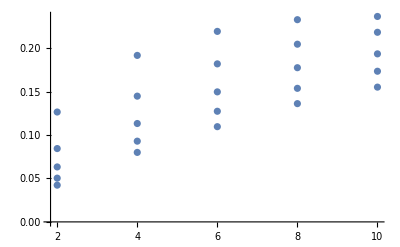

```mathematica
ListPlot[ds18⟦All,{"cmstrength","vmean"}⟧
]
```